# Grammar-based random search of trading strategies

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]
```

## Grammar definition and parsing

### Trading grammar description and possible terminals set

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["To"],{NonTerm[arg_]:>Style[arg,Bold],Term[arg_]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[Map[GrammarPrettifyRule,grammar]];
TerminalsPrettify[terminalSet_]:=Block[{gathered},
gathered = GatherBy[terminalSet/.Term[l_,v_]:>{l,v},First];
Column@Map[Style[#[[1,1]],Italic]->#[[All,2]]&,gathered]
];

grammar = {
<|"From"->"cond","To"->{Term["logicOp"],NonTerm["cond"],NonTerm["cond"]},
"Value"->Term["logicOp"]["Value"][NonTerm["cond"]["Value"],NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["not"],NonTerm["cond"]},
"Value"->Not[NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["priceQuant"],NonTerm["priceQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["priceQuant"]["Value"],NonTerm["priceQuant"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["volumeQuant"],NonTerm["volumeQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["volumeQuant"]["Value"],NonTerm["volumeQuant"]["Value"]]|>,

<|"From"->"priceQuant","To"->{Term["factor"],NonTerm["priceExpression"]},
"Value"->Times[Term["factor"]["Value"],NonTerm["priceExpression"]["Value"]]|>,

<|"From"->"priceQuant","To"->{NonTerm["priceExpression"]},
"Value"->NonTerm["priceExpression"]["Value"]|>,

<|"From"->"volumeQuant","To"->{Term["volumeValue"]},
"Value"->Term["volumeValue"]["Value"]|>,

<|"From"->"volumeQuant","To"->{NonTerm["volumeExpression"]},
"Value"->NonTerm["volumeExpression"]["Value"]|>,

<|"From"->"priceExpression","To"->{Term["techInd"],Term["observable"],Term["window"]},
"Value"->Term["techInd"]["Value"][Term["observable"]["Value"],Term["window"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["lag"],Term["observable"]},
"Value"->Prev[Term["observable"]["Value"],Term["lag"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["observable"]},
"Value"->Term["observable"]["Value"]|>,

<|"From"->"volumeExpression","To"->{Term["lag"],Term["volume"]},
"Value"->Prev[Term["volume"]["Value"],Term["lag"]["Value"]]|>,

<|"From"->"volumeExpression","To"->{Term["volume"]},
"Value"->Term["volume"]["Value"]|>
};
terminalSet = {
Term["logicOp","And"],Term["logicOp","Or"],Term["logicOp","Xor"],
Term["numOp","Greater"],Term["numOp","GreaterEqual"],Term["numOp","Less"],Term["numOp","LessEqual"],
Term["observable","Open"],Term["observable","Low"],Term["observable","High"],Term["observable","Close"],
Term["lag","1"],Term["lag","5"],Term["lag","10"],Term["lag","20"],
Term["window","2"],Term["window","5"],Term["window","10"],Term["window","15"],Term["window","20"],
Term["factor","0.5"],Term["factor","0.7"],Term["factor","0.9"],Term["factor","1.1"],Term["factor","1.3"],Term["factor","1.5"],Term["factor","2.0"],
Term["techInd","SMA"],Term["techInd","EMA"],
Term["not","Not"],Term["volume","Volume"],
Term["volumeValue","1000"],Term["volumeValue","5000"],Term["volumeValue","10000"],Term["volumeValue","50000"],Term["volumeValue","100000"],Term["volumeValue","500000"]
};
```

```mathematica
GrammarPrettify[grammar]
```

cond→{logicOp,cond,cond}
cond→{not,cond}
cond→{numOp,priceQuant,priceQuant}
cond→{numOp,volumeQuant,volumeQuant}
priceQuant→{factor,priceExpression}
priceQuant→{priceExpression}
volumeQuant→{volumeValue}
volumeQuant→{volumeExpression}
priceExpression→{techInd,observable,window}
priceExpression→{lag,observable}
priceExpression→{observable}
volumeExpression→{lag,volume}
volumeExpression→{volume}

```mathematica
TerminalsPrettify[terminalSet]
```

logicOp→{And,Or,Xor}
numOp→{Greater,GreaterEqual,Less,LessEqual}
observable→{Open,Low,High,Close}
lag→{1,5,10,20}
window→{2,5,10,15,20}
factor→{0.5,0.7,0.9,1.1,1.3,1.5,2.0}
techInd→{SMA,EMA}
not→{Not}
volume→{Volume}
volumeValue→{1000,5000,10000,50000,100000,500000}

```mathematica
GrammarGraph[grammar_]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle,ImageSize->800]
];
```

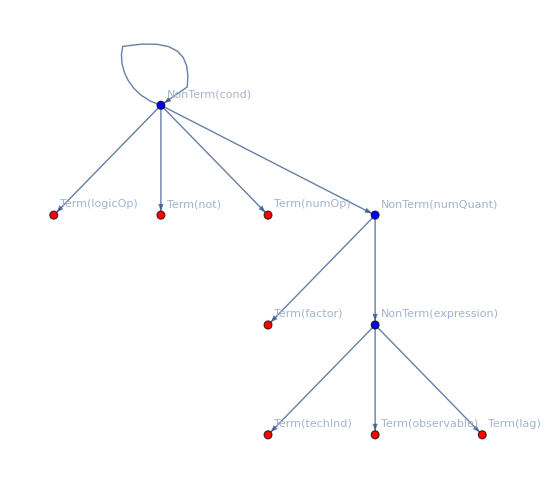

```mathematica
GrammarGraph[grammar]
```

### Expression tree synthesization

Separate head from arguments

```mathematica
GetComponents[expr_/;Depth[expr]<3]:={expr};
GetComponents[expr_/;Depth[expr]==3]:=Prepend[Level[expr,{1}],Head[expr]];
```

```mathematica
GetComponents[Less["Close",Prev[3,"Open"]]]
```

{Less,Close,Prev[3,Open]}

Rebuild expression from components

```mathematica
ExprFromComponents[components_ /;Length[components]≤1]:=First[components];
ExprFromComponents[components_ /;Length[components]>1]:=Block[{head,rest},
{head,rest} = {First[components],Rest[components]};
Apply[head,rest]
];
```

```mathematica
ExprFromComponents[{Less,"Close",Prev[3,"Open"]}] // FullForm
```

Less["Close",Prev[3,"Open"]]

Find the positions of values to be synthesized on the synthesizations list

```mathematica
GetValue[treeSymbol_,grammar_]:=ReplaceAll[treeSymbol,NonTerm[_,rule_]:>grammar[[rule]]["Value"]];
MatchPositions[expr_,synthesizations_]:=Block[{pos,newSynth,recursive},
pos = FirstPosition[synthesizations,First[expr]];
If[pos =!=Missing["NotFound"],
newSynth = ReplacePart[synthesizations,First[pos]->Found],
newSynth = synthesizations;
pos = {};
];
recursive = If[Rest[expr]≠{},MatchPositions[Rest[expr],newSynth],{}];
Transpose@{Flatten@Join[pos,recursive]}
];
```

```mathematica
synthValue = GetValue[NonTerm["expression",8],grammar]
```

Term[observable][Value]

```mathematica
MatchPositions[GetComponents[synthValue],{Term["observable"]["Value"],Term["numOp"]["Value"],Term["logicOp"]["Value"]}]
```

{{1}}

Synthesize the value of the current components from the list of synthValues.

```mathematica
Synthesize[exprComponents_,synthValues_]:=Block[{positions,lastPos,tmpSynthValues = synthValues,tmpExprComponents = exprComponents},
Do[
positions = Position[tmpSynthValues[[All,1]],tmpExprComponents[[i]]];
If[positions≠ {},
lastPos = First@Last@positions;
tmpExprComponents[[i]] = Replace[tmpExprComponents[[i]],Part[tmpSynthValues,lastPos]];
tmpSynthValues = Delete[tmpSynthValues,lastPos];
];
,{i,1,Length[tmpExprComponents]}
];
ExprFromComponents@tmpExprComponents
];
```

```mathematica
GetComponents[synthValue]
```

{Term[observable][Value]}

```mathematica
Synthesize[
GetComponents[synthValue],
Extract[{Term["observable"]["Value"]->"High",Term["numOp"]["Value"]->"Greater",Term["logicOp"]["Value"]->"And"},{{1}}]
]
```

High

Synthesize terminals and nonterminals.

```mathematica
SynthesizeNonTerm[treeSymbol_,grammar_,synthesizations_]:=Block[{val,components,eval,matchPos,newSynth,newSynthLabel},
val = GetValue[treeSymbol,grammar];
components = GetComponents[val];
matchPos = MatchPositions[components,synthesizations[[All,1]]];
eval = Synthesize[components,Extract[synthesizations,matchPos]];
newSynth = Delete[synthesizations,matchPos];
newSynthLabel = ReplaceAll[treeSymbol,NonTerm[x_,_]:>NonTerm[x]["Value"]];

Prepend[newSynth,newSynthLabel->eval]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]==2,
Prepend[synthesizations, ReplaceAll[treeSymbol,Term[termName_,value_]:>(Term[termName]["Value"]->value)]],
synthesizations
]
];
```

Complete tree synthesization.

```mathematica
SynthesizeTree[graph_,labels_,grammar_]:=Block[{depthFirstScan,labeledDFS,symbolType,synthesized},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[s];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,grammar,synthesized]];
,
{s,labeledDFS}
];

ToExpression@ToString@Return[synthesized[[1,-1]]] /.{Open->"Open",High->"High",Low->"Low",Close->"Close",Volume->"Volume"}
];
SynthesizeTree[{graph_,labels_}]:=SynthesizeTree[graph,labels,grammar];

FormatStep[step_]:=Column[{
Style["Next symbol:",Bold],
step[[1]],
Style["Next production:",Bold],
step[[2]],
Style["Synthesized:",Bold],
step[[3]],
Style["Tree:",Bold],
step[[4]]
}];
ViewSynthesization[graph_,labels_,grammar_]:=DynamicModule[{depthFirstScan,labeledDFS,symbolType,synthesized,synthesis,formattedSynthesis},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
synthesis = First@Last@Reap@Do[
symbolType = Head[labeledDFS[[i]]];
If[symbolType === Term,synthesized = SynthesizeTerm[labeledDFS[[i]],synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[labeledDFS[[i]],grammar,synthesized]];

If[i!=Length[depthFirstScan],
Sow[{labeledDFS[[i+1]],GetValue[labeledDFS[[i+1]],grammar],synthesized,VertexDelete[graph,Take[depthFirstScan,{1,i}]]}],
Sow[{None,None,synthesized,VertexDelete[graph,Take[depthFirstScan,{1,i}]]}]
];
,
{i,1,Length[depthFirstScan],1}
];

formattedSynthesis = Map[FormatStep,synthesis];

Manipulate[formattedSynthesis[[i]],{i,1,Length[formattedSynthesis],1},SaveDefinitions->True]
];
```

```mathematica
{g,l} = GenerateRandomFunction[grammar,terminalSet,100];
ViewSynthesization[g,l,grammar]
```

## Operations on trees

Tree manipulations operations.

```mathematica
RestartLabelsAt[graph_,labels_,startNum_ : 1]:=Block[{replaceRules,newEdges,newLabels},
replaceRules = Thread[VertexList[graph]->Range[startNum,startNum+Length[VertexList[graph]]-1]];
newEdges = EdgeList[graph]/.replaceRules;
newLabels = MapAt[#/.replaceRules&,labels,{All,1}];

{Graph[newEdges,VertexLabels->newLabels,ImageSize->500],newLabels}
];
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->newLabels,ImageSize->500],newLabels}
];

InsertSubtree[graph_,labels_,subtree_,sublabels_]:=Block[{missingVertexes,edges,missing,splitPos,left,right,middleRules,formattedSubtreeRoot,remaining,rightRules,newLeftGraph,newMiddleGraph,newRightGraph,insertLabels,incompleteLabels,newEdges,newLabels,newRootForSub,newRightLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missingVertexes = Complement[Range[Max[edges]],edges];
If[missingVertexes ≠ {},
missing =  First@missingVertexes;
splitPos = First@FirstPosition[EdgeList[graph],_->Empty];
{left,right} = TakeDrop[EdgeList[graph],splitPos];

middleRules = Thread[VertexList[subtree]->(VertexList[subtree]+missing-1)];
newMiddleGraph = EdgeList[subtree]/.middleRules;
formattedSubtreeRoot = 1 /.middleRules;

remaining = Complement[VertexList[right],VertexList[left]];
rightRules = Thread[remaining->(remaining+Max[VertexList[newMiddleGraph]]-Min[remaining]+1)];

newLeftGraph = left/.Empty->formattedSubtreeRoot;
newRightGraph = right /.rightRules;
insertLabels = MapAt[#/.middleRules&,sublabels,{All,1}];
incompleteLabels = MapAt[#/.rightRules&,labels,{All,1}];

newEdges = Join[newLeftGraph,newMiddleGraph,newRightGraph];
newLabels = SortBy[Join[incompleteLabels,insertLabels],First];

,

newRootForSub = Max[DeleteCases[VertexList[graph],Empty]]+1;
{newRightGraph,newRightLabels} = RestartLabelsAt[subtree,sublabels,newRootForSub];
newEdges = Join[EdgeList[graph]/.Empty->newRootForSub,EdgeList[newRightGraph]];
newLabels = Join[labels,newRightLabels];
];

{Graph[newEdges,VertexLabels->newLabels,ImageSize->500],newLabels}
];
```

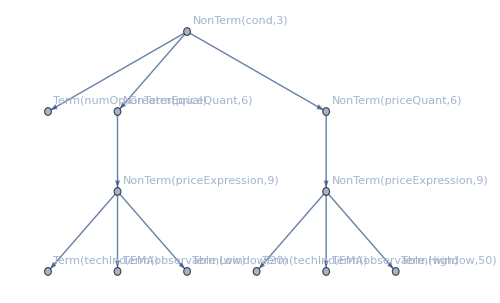
```mathematica
{g1,labels1} = {-Graphics-,{1->NonTerm["cond",3],2->Term["numOp","GreaterEqual"],3->NonTerm["priceQuant",6],4->NonTerm["priceExpression",9],5->Term["techInd","EMA"],6->Term["observable","Low"],7->Term["window","20"],8->NonTerm["priceQuant",6],9->NonTerm["priceExpression",9],10->Term["techInd","EMA"],11->Term["observable","High"],12->Term["window","50"]}};
```

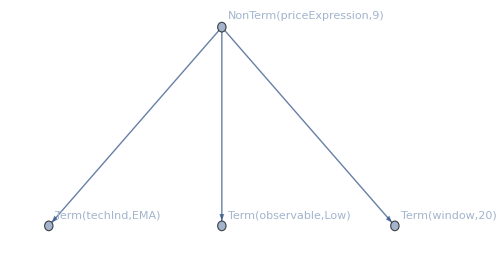
{-Graphics-,{1→NonTerm[priceExpression,9],2→Term[techInd,EMA],3→Term[observable,Low],4→Term[window,20]}}

```mathematica
subtree1 = Apply[RestartLabelsAt,Subtree[g1,labels1,4]]
```

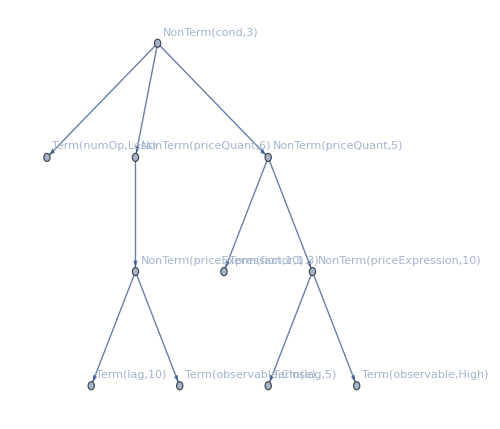
```mathematica
{g2,labels2} = {-Graphics-,{1->NonTerm["cond",3],2->Term["numOp","Less"],3->NonTerm["priceQuant",6],4->NonTerm["priceExpression",10],5->Term["lag","10"],6->Term["observable","Close"],7->NonTerm["priceQuant",5],8->Term["factor","1.3"],9->NonTerm["priceExpression",10],10->Term["lag","5"],11->Term["observable","High"]}};
```

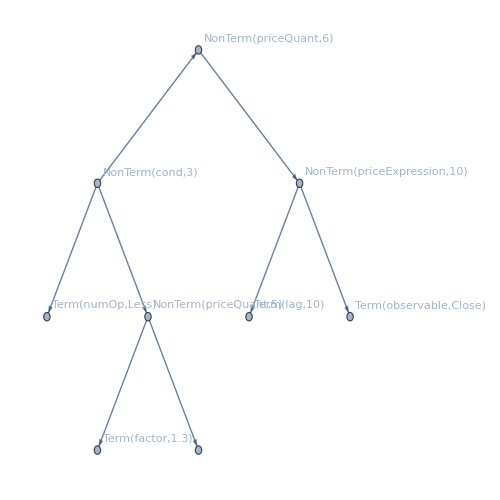
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,10],5→Term[lag,10],6→Term[observable,Close],7→NonTerm[priceQuant,5],8→Term[factor,1.3]}}

```mathematica
cropped2 = DeleteSubtree[g2,labels2,9]
```

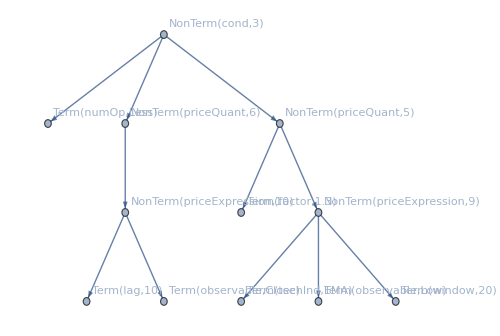
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,10],5→Term[lag,10],6→Term[observable,Close],7→NonTerm[priceQuant,5],8→Term[factor,1.3],9→NonTerm[priceExpression,9],10→Term[techInd,EMA],11→Term[observable,Low],12→Term[window,20]}}

```mathematica
inserted = InsertSubtree[First[cropped2],Last[cropped2],First[subtree1],Last[subtree1]]
```

```mathematica
SynthesizeTree[First[inserted],Last[inserted],grammar] // FullForm
```

Less[Prev["Close",10],Times[1.3,EMA["Low",20]]]

## Population initialization

```mathematica
NonTermName[nonterm_]:=ReplaceAll[nonterm,NonTerm[x_]:>x];
NonTermWithProd[nonterm_,prodIndex_]:=NonTerm[NonTermName[nonterm],prodIndex];
ApplicableProductions[nonterm_,grammar_]:=First@Transpose@Position[grammar,KeyValuePattern["From"->NonTermName[nonterm]]];
UnassignedProductionQ[prod_]:=MatchQ[prod,NonTerm[_]];

ProductionRuleAsGraph[grammar_,prodIndex_]:=Block[{rootNonTerm,newLeafs,edgeList,vertexLabels},
rootNonTerm = NonTermWithProd[NonTerm[grammar[[prodIndex]]["From"]],prodIndex];
newLeafs = grammar[[prodIndex]]["To"];
edgeList = Thread[1->Range[2,1+Length[newLeafs]]];
vertexLabels = Prepend[Thread[Range[2,1+Length[newLeafs]]->newLeafs],1->rootNonTerm];

{Graph[edgeList,VertexLabels->vertexLabels],vertexLabels}
];

GrowTree[graph_,labels_,grammar_,maxDepth_]:=Block[{unassignedVertexes,replaceIndex,cropped,replaceNonTerm,selectedProduction,sub,new},
If[graph===$Failed || labels ===$Failed,Return[{$Failed,$Failed}]];

unassignedVertexes = Cases[labels,HoldPattern[v_->t_ /; UnassignedProductionQ[t]]:>v];
replaceIndex = RandomChoice[unassignedVertexes];
cropped = DeleteSubtree[graph,labels,replaceIndex];
replaceNonTerm = Last[labels[[replaceIndex]]];
selectedProduction = RandomChoice[ApplicableProductions[replaceNonTerm,grammar]];
sub = ProductionRuleAsGraph[grammar,selectedProduction];
new = InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]];

If[Length[Last[new]]<100,new,{$Failed,$Failed}]
];

GenerateRandomTree[grammar_,maxDepth_]:=Block[{tree},
tree =ProductionRuleAsGraph[grammar,RandomInteger[{1,3}]];
NestWhile[
GrowTree[First[#],Last[#],grammar,maxDepth]&,tree,#=!={$Failed,$Failed}&&Apply[Or,Map[UnassignedProductionQ,Cases[Last[#][[All,2]],_NonTerm]]]&
]
];
RandomTerm[name_,terminalSet_]:=RandomChoice[Cases[terminalSet,Term[name,_]]];
GenerateRandomTerminals[labels_,terminalSet_]:=ReplaceAll[labels,HoldPattern[v_->Term[n_]]:>(v->RandomTerm[n,terminalSet])];

GenerateRandomFunction[grammar_,terminalSet_,maxDepth_]:=Block[{g=$Failed,l=$Failed,labelsWithTerminals},
While[g===$Failed || l ===$Failed,
{g,l} = GenerateRandomTree[grammar,maxDepth];
];
labelsWithTerminals = GenerateRandomTerminals[l,terminalSet];

{EdgeList[g],labelsWithTerminals}
];
GenerateRandomFunction[maxDepth_]:=GenerateRandomFunction[grammar,terminalSet,maxDepth];
```

```mathematica
{g,l} = GenerateRandomFunction[grammar,terminalSet,100]
SynthesizeTree[g,l,grammar] // FullForm
```

{{1->2,1->3,3->4,3->5,5->6,5->7,7->8,7->9,9->10,9->11,11->12,9->13,13->14,14->15,14->16,1->17,17->18,17->19,19->20,19->21,21->22,21->23,23->24,23->25,25->26,25->27,27->28,27->29,23->30,30->31,31->32,31->33,31->34,17->35,35->36,35->37,37->38,37->39,39->40,37->41,41->42},{1→NonTerm[cond,1],2→Term[logicOp,Or],3→NonTerm[cond,2],4→Term[not,Not],5→NonTerm[cond,2],6→Term[not,Not],7→NonTerm[cond,2],8→Term[not,Not],9→NonTerm[cond,4],10→Term[numOp,Less],11→NonTerm[volumeQuant,7],12→Term[volumeValue,500000],13→NonTerm[volumeQuant,8],14→NonTerm[volumeExpression,12],15→Term[lag,1],16→Term[volume,Volume],17→NonTerm[cond,1],18→Term[logicOp,Xor],19→NonTerm[cond,2],20→Term[not,Not],21→NonTerm[cond,2],22→Term[not,Not],23→NonTerm[cond,3],24→Term[numOp,Less],25→NonTerm[priceQuant,5],26→Term[factor,0.5],27→NonTerm[priceExpression,10],28→Term[lag,5],29→Term[observable,Low],30→NonTerm[priceQuant,6],31→NonTerm[priceExpression,9],32→Term[techInd,EMA],33→Term[observable,High],34→Term[window,10],35→NonTerm[cond,2],36→Term[not,Not],37→NonTerm[cond,4],38→Term[numOp,Greater],39→NonTerm[volumeQuant,7],40→Term[volumeValue,100000],41→NonTerm[volumeQuant,7],42→Term[volumeValue,5000]}}

Or[GreaterEqual[500000,Prev["Volume",1]],Less[Times[0.5,Prev["Low",5]],EMA["High",10]]]

## Fitness function

### Database creation

```mathematica
dateFolders = Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV"}]],FileExtension[#]==""&];
```

```mathematica
dates = Map[FileBaseName,dateFolders]
```

{2020-01-20,2020-01-21,2020-01-22,2020-01-23,2020-01-24,2020-01-27,2020-01-28,2020-01-29,2020-01-30,2020-01-31,2020-02-04,2020-02-05,2020-02-06,2020-02-07,2020-02-10,2020-02-11,2020-02-12,2020-02-13,2020-02-14,2020-02-17,2020-02-18,2020-02-19,2020-02-20,2020-02-25,2020-02-26,2020-02-27}

```mathematica
{trainingDates,validationDates} = TakeDrop[dates,Ceiling[0.8Length[dates]]];
```

```mathematica
stockPaths = FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",First[dates]}]];
stocks = Map[FileBaseName,stockPaths]
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
AdaptativeMovingAverage[maFunc_,list_,r_]:=Join[Table[First@maFunc[Take[list,n],n],{n,1,r-1}],maFunc[list,r]];
LaggedList[list_,lag_]:=Join[ConstantArray[First[list],lag],Drop[list,-lag]];

BuildDerivatives[dataset_]:=Block[{keys,windows,obsWindowTuples,sma,ema,lags,obsLagTuples,prev,derivatives,derivativesData},
keys = Keys[First[dataset]];
windows = Cases[terminalSet,Term["window",l_]:>ToExpression[l]];
obsWindowTuples = Tuples[{keys,windows}];
lags = Cases[terminalSet,Term["lag",l_]:>ToExpression[l]];
obsLagTuples = Tuples[{keys,lags}];

sma =Map[Apply[SMA,#]->AdaptativeMovingAverage[MovingAverage,dataset[[All,First[#]]],Last[#]]&,obsWindowTuples];
ema =Map[Apply[EMA,#]->ExponentialMovingAverage[dataset[[All,First[#]]],Last[#]/50]&,obsWindowTuples];
prev = Map[Apply[Prev,#]->LaggedList[dataset[[All,First[#]]],Last[#]]&,obsLagTuples];
derivatives = Map[Thread,Join[sma,ema,prev]];
derivativesData = Map[Association,Transpose[derivatives]];

MapThread[Join,{derivativesData,dataset}]

];
```

```mathematica
CreateTick[{open_,high_,low_,close_,volume_}]:=<|"Open"->open,"High"->high,"Low"->low,"Close"->close,"Volume"->volume|>;
CreateTickDatabase[date_,stock_]:=Block[{path,dataset},
path = FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",date}];
dataset = DeleteCases[Import[FileNameJoin[{path,StringJoin[stock,".csv"]}]],{_,"","","","",""}];

BuildDerivatives@Map[CreateTick[Drop[#,1]]&,Drop[dataset,1]]
];
CreateMarketDailyDatabase[date_,stocks_]:=Association[ProgressMap[#->CreateTickDatabase[date,#]&,stocks]];
```

```mathematica
databaseFile = FileNameJoin[{NotebookDirectory[],"gp_database.mx"}];
If[FileExistsQ[databaseFile],
stockDatabase = Import[databaseFile],

stockDatabase = ProgressMap[CreateMarketDailyDatabase[#,stocks]&,dates];
Export[databaseFile,stockDatabase];
];
```

```mathematica
First@stockDatabase[[1,"AC.MX"]]
```

<|SMA[Open,10]→105.13,SMA[Open,20]→105.13,SMA[Open,30]→105.13,SMA[Open,40]→105.13,SMA[Open,50]→105.13,SMA[High,10]→106.43,SMA[High,20]→106.43,SMA[High,30]→106.43,SMA[High,40]→106.43,SMA[High,50]→106.43,SMA[Low,10]→105.13,SMA[Low,20]→105.13,SMA[Low,30]→105.13,SMA[Low,40]→105.13,SMA[Low,50]→105.13,SMA[Close,10]→105.99,SMA[Close,20]→105.99,SMA[Close,30]→105.99,SMA[Close,40]→105.99,SMA[Close,50]→105.99,SMA[Volume,10]→0.,SMA[Volume,20]→0.,SMA[Volume,30]→0.,SMA[Volume,40]→0.,SMA[Volume,50]→0.,EMA[Open,10]→105.13,EMA[Open,20]→105.13,EMA[Open,30]→105.13,EMA[Open,40]→105.13,EMA[Open,50]→105.13,EMA[High,10]→106.43,EMA[High,20]→106.43,EMA[High,30]→106.43,EMA[High,40]→106.43,EMA[High,50]→106.43,EMA[Low,10]→105.13,EMA[Low,20]→105.13,EMA[Low,30]→105.13,EMA[Low,40]→105.13,EMA[Low,50]→105.13,EMA[Close,10]→105.99,EMA[Close,20]→105.99,EMA[Close,30]→105.99,EMA[Close,40]→105.99,EMA[Close,50]→105.99,EMA[Volume,10]→0.,EMA[Volume,20]→0.,EMA[Volume,30]→0.,EMA[Volume,40]→0.,EMA[Volume,50]→0.,Prev[Open,1]→105.13,Prev[Open,5]→105.13,Prev[Open,10]→105.13,Prev[Open,25]→105.13,Prev[Open,50]→105.13,Prev[High,1]→106.43,Prev[High,5]→106.43,Prev[High,10]→106.43,Prev[High,25]→106.43,Prev[High,50]→106.43,Prev[Low,1]→105.13,Prev[Low,5]→105.13,Prev[Low,10]→105.13,Prev[Low,25]→105.13,Prev[Low,50]→105.13,Prev[Close,1]→105.99,Prev[Close,5]→105.99,Prev[Close,10]→105.99,Prev[Close,25]→105.99,Prev[Close,50]→105.99,Prev[Volume,1]→0.,Prev[Volume,5]→0.,Prev[Volume,10]→0.,Prev[Volume,25]→0.,Prev[Volume,50]→0.,Open→105.13,High→106.43,Low→105.13,Close→105.99,Volume→0.|>

### Backtesting implementation

```mathematica
StrategyValues[strategyFunc_,tradingDayData_]:=Map[ReplaceAll[strategyFunc,#]&,tradingDayData];
StrategySignals[strategyFunc_,tradingDayData_]:=Block[{strategyValues,signals},
strategyValues = Join[Drop[StrategyValues[strategyFunc,tradingDayData],-2],{False,False}]; (* Always sell at the end *)
signals = Flatten[Map[
Join[
{First[#]/.{True->"Enter",False->"Exit"}},
ConstantArray["Hold",Length[#]-1]
]&,Split[strategyValues]
]
];

If[First[signals]=="Exit",ReplacePart[signals,1->"Hold"],signals]
];
StrategyReturn[strategyFunc_,tradingDayData_,transactionCost_]:=Block[{signals,enterPositions,exitPositions,buyPrices,sellPrices},
signals = StrategySignals[strategyFunc,tradingDayData];
enterPositions = Position[Drop[signals,-2],"Enter"]+1;
exitPositions = Position[Drop[signals,-1],"Exit"]+1;
If[enterPositions=={} || exitPositions == 0,Return[0.0]];

buyPrices = Extract[tradingDayData,enterPositions][[All,"Open"]];
sellPrices = Extract[tradingDayData,exitPositions][[All,"Open"]];

Total[Log[sellPrices(1-transactionCost)]]-Total[Log[buyPrices(1+transactionCost)]]
];
StrategyReturnOverMarket[strategyFunc_,date_,transactionCost_]:=Total@Map[StrategyReturn[strategyFunc,stockDatabase[[date,#]],transactionCost]&,stocks];
StrategyPerformanceOverTime[strategyFunc_,tradingDayData_,transactionCost_]:=Block[{signals,balance,laggedSignals},
signals = StrategySignals[strategyFunc,tradingDayData];
balance = 0;
laggedSignals = Prepend[Drop[signals,-1],Last[signals]];

Table[
If[laggedSignals[[i]]=="Enter",balance -= tradingDayData[[i]]["Open"]*(1+transactionCost)];
If[laggedSignals[[i]]=="Exit",balance += tradingDayData[[i]]["Open"]*(1-transactionCost)];
balance
,{i,1,Length[tradingDayData]}
]
];
```

```mathematica
strategyFunc = Or[Less[Times[1.05,SMA["Close",20]],SMA["Close",40]],Less[Prev["Close",2],"High"]];
```

```mathematica
tradingDayData = stockDatabase[[1,"AC.MX"]];
```

```mathematica
StrategyValues[strategyFunc,tradingDayData]
```

{True,True,True,False,False,True,True,True,False,False,True,True,True,True,False,False,False,True,False,False,False,False,True,True,True,False,True,True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,True,False,False,True,False,True,True,True,False,False,False,True,True,True,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,True,True,True,False,True,True,False,False,False,False,False,False,True,True,False,True,False,False,True,False,False,False,False,True,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,True,True,True,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,True,True,True,True}

```mathematica
signals = StrategySignals[strategyFunc,tradingDayData]
```

{Enter,Hold,Hold,Exit,Hold,Enter,Hold,Hold,Exit,Hold,Enter,Hold,Hold,Hold,Exit,Hold,Hold,Enter,Exit,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Enter,Exit,Enter,Hold,Hold,Exit,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Enter,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Enter,Exit,Hold,Enter,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Enter,Hold,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Exit,Enter,Hold,Hold,Hold,Hold,Hold,Exit,Hold}

```mathematica
StrategyReturn[strategyFunc,tradingDayData,0.0025]
```

-4.79954

## Random search 1

```mathematica
TestStrategy[strategyFunc_,dayIndex_,stocks_,transactionCost_ : 0.0]:=Map[StrategyReturn[strategyFunc,stockDatabase[[dayIndex,#]],transactionCost]&,stocks];
```

```mathematica
useStocks = {"AC.MX","KOFUBL.MX"};
```

```mathematica
randomStrategies = ProgressTable[
Block[{g,l,expr},
{g,l} = GenerateRandomFunction[grammar,terminalSet,350];
expr = SynthesizeTree[g,l,grammar] ;
{{g,l},Total@Flatten@Table[TestStrategy[expr,i,useStocks,0.0005],{i,1,20}]}
],
30000
];
```

```mathematica
strategiesSorted = Reverse@SortBy[randomStrategies,Last];
```

```mathematica
Map[{SynthesizeTree[First[First[#]],Last[First[#]],grammar],Last[#]}&,strategiesSorted[[1;;3]]]
```

{{EMA[Close,10]<EMA[High,10],0.013272},{EMA[High,5]>EMA[Close,5],0.013272},{EMA[High,15]>EMA[Close,15],0.013272}}

```mathematica
seeds = strategiesSorted[[1;;3]][[All,1]];
```

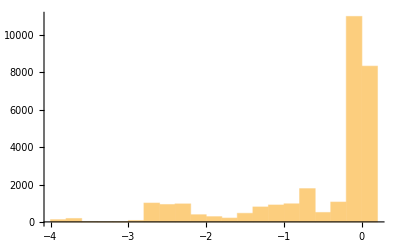

```mathematica
Histogram[strategiesSorted[[All,2]]]
```

```mathematica
SynthesizeTree[First[First[strategiesSorted]]]
```

EMA[Close,10]<EMA[High,10]

```mathematica
results = ProgressTable[TestStrategy[SynthesizeTree[First[First[strategiesSorted]]],i,useStocks],{i,1,Length[dates]}]
```

{{-0.00603376,0.00472208},{0.00331297,0.00448196},{0.00150847,0.0167477},{0.016032,-0.00754144},{-0.0108363,0.000760265},{-0.00181077,-0.0160265},{0.0131252,0.00381345},{0.00569058,0.00971136},{0.00906677,0.000692471},{-0.00614867,-0.00640194},{0.00995211,0.00272781},{-0.0190992,-0.000592941},{-0.000835265,0.00835065},{0.00920036,0.00969505},{-0.00484801,-0.00257848},{0.00018586,0.00671837},{-0.0136043,-0.00836757},{-0.0100494,-0.0051913},{0.0324293,0.0070393},{0.00190796,-0.00463409},{-0.000454677,-0.00400832},{0.000722625,-0.00902257},{0.0077464,-0.0173888},{0.00455582,-0.00714043},{-0.00496052,-0.00685987},{-0.00466201,-0.0373321}}

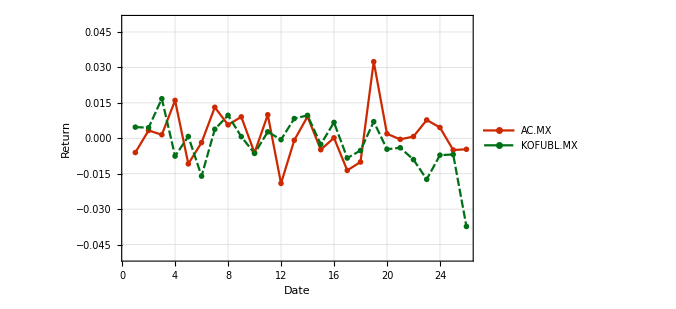

```mathematica
ListLinePlot[
Transpose[results],PlotRange->{All,{-0.05,0.05}},
PlotLegends->useStocks,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",15], Style["Return",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.44, 0.09],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
]
```

## Random search 2

```mathematica
TestStrategy[strategyFunc_,dayIndex_,stocks_,transactionCost_ : 0.0]:=Map[StrategyReturn[strategyFunc,stockDatabase[[dayIndex,#]],transactionCost]&,stocks];
```

```mathematica
useStocks = stocks;
```

```mathematica
randomStrategies = ProgressTable[
Block[{g,l,expr},
{g,l} = GenerateRandomFunction[350];
expr = SynthesizeTree[{g,l}] ;
{{g,l},Total@Flatten@Table[TestStrategy[expr,i,useStocks,0.0005],{i,1,20}]}
],
5000
];
```

```mathematica
strategiesSorted = Reverse@SortBy[randomStrategies,Last];
```

```mathematica
Map[{SynthesizeTree[First[First[#]],Last[First[#]],grammar],Last[#]}&,strategiesSorted[[1;;3]]]
```

{{((!(0.7 Prev[Open,20]≥Open&&High≤0.9 EMA[Open,20])⊻!((500000≤Volume&&0.7 Open<0.7 SMA[Low,5])⊻10000>Prev[Volume,1]))||Volume<10000||Volume<100000)&&1.5 EMA[High,15]≤EMA[High,10],0.},{!((1.3 Close≥EMA[High,5]&&Volume≥Volume)||(1.5 SMA[Open,20]≥1.1 High&&(0.5 Low>Close⊻1.3 Prev[Low,20]≤Prev[Low,20])&&(Close>0.7 Prev[Close,1]⊻EMA[High,15]<1.1 Open))),0.},{False,0.}}

```mathematica
seeds = strategiesSorted[[1;;3]][[All,1]];
```

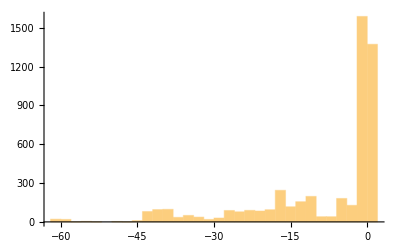

```mathematica
Histogram[strategiesSorted[[All,2]]]
```

```mathematica
SynthesizeTree[First[First[strategiesSorted]]]
```

(Prev[Volume,10]>100000&&1.3 SMA[Open,10]≥0.9 Low&&Volume≥500000&&SMA[High,20]≤EMA[Low,5])⊻SMA[Low,15]>2. Open

```mathematica
results = ProgressTable[TestStrategy[SynthesizeTree[First[First[strategiesSorted]]],i,useStocks],{i,1,Length[dates]}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

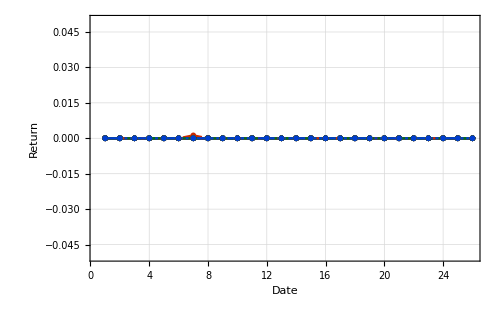

```mathematica
ListLinePlot[
Transpose[results],PlotRange->{All,{-0.05,0.05}},
PlotLegends->useStocks,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",15], Style["Return",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.44, 0.09],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
]
```